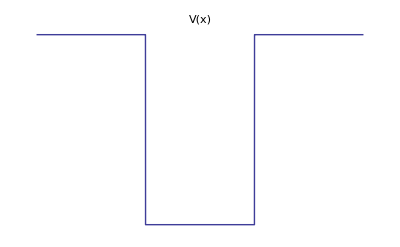

```mathematica
ClearAll["Global`*"]
v[x_ /; Abs[x] > 1] := 0
v[x_ /; Abs[x] < 1] := -1
Plot[v[x], { x, -3, 3}, PlotLabel  -> V[x], Axes ->False ]
```

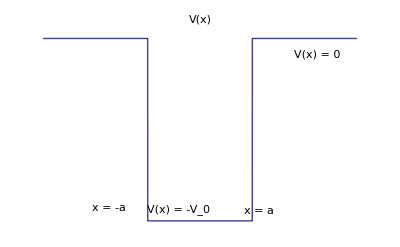

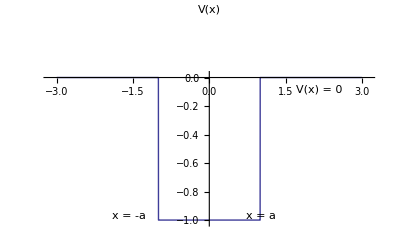

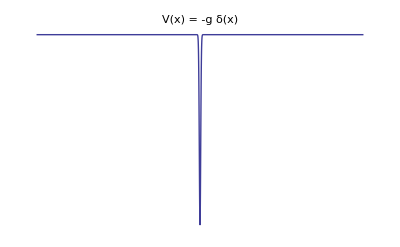

```mathematica
a:= 0.3
Plot[-Exp[- x^2/a^2]/Sqrt[a^2 Pi], {x, -50, 50}, Axes -> False, PlotLabel -> "V(x) = -g δ(x)"]
```